# HighPT

## Flavor bounds from high-p_T tails at LHC

Keep this notebook out of git !!!

## Preamble

#### Set package directory

Make sure that the package directory is in the $Path.

```mathematica
SetDirectory@ ParentDirectory@ NotebookDirectory[];
(*AppendTo[$Path, "/path/to/HighPT"];*)
```

#### Loading the package

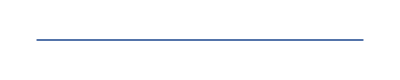

HighPT | : | High-p_T Tails
 |  | 
Authors | : | Lukas Allwicher, Darius A. Faroughy, Florentin Jaffredo,
 |  | Olcyr Sumensari, and Felix Wilsch
Reference | : | arXiv:22xx.xxxxxhttps://arxiv.org/Nonehttps://arxiv.org/HyperlinkHyperlinkActive
Website | : | https://github.com/HighPT/HighPThttps://github.com/HighPT/HighPTNonehttps://github.com/HighPT/HighPTHyperlinkHyperlinkActive

HighPT is free software under the terms of the MIT License.

Please submit bugs and feature requests using GitHub's issue system at:

https://github.com/HighPT/HighPT/issueshttps://github.com/HighPT/HighPT/issuesNonehttps://github.com/HighPT/HighPT/issuesHyperlinkHyperlinkActive

-Graphics-

Using model: SMEFT

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

```mathematica
<<HighPT`
```

#### FOR DEVELOPMENT ONLY

This allows to access all PackageScope functions in the notebook.
Remove this line eventually.

```mathematica
PrependTo[$ContextPath, "HighPT`PackageScope`"];
```

## Overview of all functions

```mathematica
?HighPT`*
```

## Cross sections

## Differential hadronic cross section dσ/ds

```mathematica
?DifferentialCrossSection
```

#### Derive dσ/ds as a function of s

```mathematica
σDiff=DifferentialCrossSection[
	{e[3],e[3]},
	OutputFormat-> {"SMEFT",1000},
	Coefficients-> {WC["Hl1",{3,3}],WC["lq1",{3,3,3,3}]}
];
```

#### Plot the cross section for different values of the Wilson coefficients

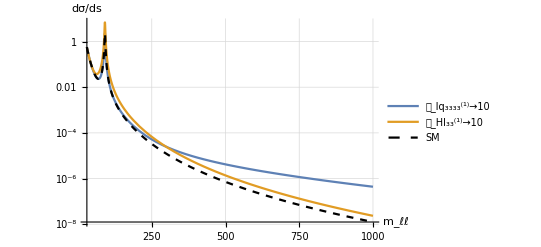

```mathematica
LogPlot[
	{
		σDiff[mll^2]/.{WC["lq1",{3,3,3,3}]->10,WC["Hl1",{3,3}]->0},
		σDiff[mll^2]/.{WC["lq1",{3,3,3,3}]->0,WC["Hl1",{3,3}]->10},
		σDiff[mll^2]/.{WC["lq1",{3,3,3,3}]->0,WC["Hl1",{3,3}]->0}
	},
	{mll,30,1000}
	,
	PlotLegends->{WC["lq1",{3,3,3,3}]->10, WC["Hl1",{3,3}]->10, "SM"},
	PlotStyle->{Automatic,Automatic,{Black,Dashed}},
	AxesLabel->{"m_ℓℓ","dσ/ds"},
	PlotRange->Full,
	Background->White,
	GridLines->Automatic
]
```

## Total hadronic cross section

```mathematica
?CrossSection
```

#### Compute cross section for pp→τ^-ν̄ in the bin m_ℓℓ∈{1 TeV, 5 TeV} and p_T∈{50 GeV,∞}

```mathematica
σTot=EchoTiming@CrossSection[
	{e[3],ν},
	MLLcuts->{1000,5000},
	PTcuts->{50,∞}
]
```

45.0338

(0.+0. ⅈ)+0.0438218 Conjugate[FF[DipoleL,{WBoson,0},{Left,Left},{e[3],ν[1],u[1],d[1]}]] FF[DipoleL,{WBoson,0},{Left,Left},{e[3],ν[1],u[1],d[1]}]+1608+(3.87613×10^-6+2.60449×10^-24 ⅈ) Conjugate[FF[Vector,{WBoson,SM},{Left,Left},{e[3],ν[3],u[3],d[3]}]] FF[Vector,{WBoson,SM},{Left,Left},{e[3],ν[3],u[3],d[3]}]
 |  |  |  |

#### Print partial results (e.g. only scalar form factors)

```mathematica
TraditionalForm[σTot/.FF[Except[Scalar],___]->0]
```

62.0137 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[1]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LL]_(u[1]d[1])^(e[3]ν[1])+7.50958 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[1]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LL]_(u[1]d[2])^(e[3]ν[1])+2.74883 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[1]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LL]_(u[1]d[3])^(e[3]ν[1])+30.0878 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[2]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LL]_(u[2]d[1])^(e[3]ν[1])+3.447 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[2]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LL]_(u[2]d[2])^(e[3]ν[1])+1.22279 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[2]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LL]_(u[2]d[3])^(e[3]ν[1])+62.0137 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[1]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LL]_(u[1]d[1])^(e[3]ν[2])+7.50958 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[1]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LL]_(u[1]d[2])^(e[3]ν[2])+2.74883 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[1]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LL]_(u[1]d[3])^(e[3]ν[2])+30.0878 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[2]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LL]_(u[2]d[1])^(e[3]ν[2])+3.447 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[2]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LL]_(u[2]d[2])^(e[3]ν[2])+1.22279 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[2]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LL]_(u[2]d[3])^(e[3]ν[2])+62.0137 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[1]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LL]_(u[1]d[1])^(e[3]ν[3])+7.50958 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[1]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LL]_(u[1]d[2])^(e[3]ν[3])+2.74883 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[1]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LL]_(u[1]d[3])^(e[3]ν[3])+30.0878 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[2]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LL]_(u[2]d[1])^(e[3]ν[3])+3.447 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[2]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LL]_(u[2]d[2])^(e[3]ν[3])+1.22279 Conjugate[([F_(S{reg,{0,0}})^LL]_(u[2]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LL]_(u[2]d[3])^(e[3]ν[3])+60.4167 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[1])+7.04572 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[1])-(0.195932+0.20323 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[1])+7.3061 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[1])+0.89657 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[1])-(0.0219227+0.0246102 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[1])+2.67235 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[1])+0.336782 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[1])-(0.00766702+0.00900842 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[1])+7.04572 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[1])+31.7455 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[1])+(1.2068-0.0472434 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[1])+0.89657 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[1])+3.65769 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[1])+(0.138379-0.00572097 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[1])+0.336782 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[1])+1.30189 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[1])+(0.0491142-0.00209412 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[1])-(0.195932-0.20323 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[1])+(1.2068+0.0472434 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[1])+(0.0502327+0. ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[1])-(0.0219227-0.0246102 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[1])+(0.138379+0.00572097 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[1])+(0.00576019+0. ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[1])-(0.00766702-0.00900842 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[1])+(0.0491142+0.00209412 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[1])+(0.00204449+0. ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[1]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[1])+60.4167 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[2])+7.04572 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[2])-(0.195932+0.20323 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[2])+7.3061 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[2])+0.89657 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[2])-(0.0219227+0.0246102 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[2])+2.67235 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[2])+0.336782 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[2])-(0.00766702+0.00900842 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[2])+7.04572 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[2])+31.7455 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[2])+(1.2068-0.0472434 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[2])+0.89657 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[2])+3.65769 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[2])+(0.138379-0.00572097 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[2])+0.336782 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[2])+1.30189 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[2])+(0.0491142-0.00209412 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[2])-(0.195932-0.20323 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[2])+(1.2068+0.0472434 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[2])+(0.0502327+0. ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[2])-(0.0219227-0.0246102 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[2])+(0.138379+0.00572097 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[2])+(0.00576019+0. ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[2])-(0.00766702-0.00900842 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[2])+(0.0491142+0.00209412 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[2])+(0.00204449+0. ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[2]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[2])+60.4167 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[3])+7.04572 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[3])-(0.195932+0.20323 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[3])+7.3061 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[3])+0.89657 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[3])-(0.0219227+0.0246102 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[3])+2.67235 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[3])+0.336782 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[3])-(0.00766702+0.00900842 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[3])+7.04572 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[3])+31.7455 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[3])+(1.2068-0.0472434 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[3])+0.89657 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[3])+3.65769 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[3])+(0.138379-0.00572097 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[3])+0.336782 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[3])+1.30189 Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[3])+(0.0491142-0.00209412 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[3])-(0.195932-0.20323 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[3])+(1.2068+0.0472434 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[3])+(0.0502327+0. ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[1])^(e[3]ν[3])-(0.0219227-0.0246102 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[3])+(0.138379+0.00572097 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[3])+(0.00576019+0. ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[2])^(e[3]ν[3])-(0.00766702-0.00900842 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[1]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[3])+(0.0491142+0.00209412 ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[2]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[3])+(0.00204449+0. ⅈ) Conjugate[([F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[3]))] [F_(S{reg,{0,0}})^LR]_(u[3]d[3])^(e[3]ν[3])+(0.+0. ⅈ)

## Event yield per bin in observable

```mathematica
?EventYield
```

#### Number of events for each bin in the observable (m_T^tot) as a function of the form factors

```mathematica
LoadEfficiencies["tata"]
```

{Efficiency[dipole,{Photon,Photon},{0,0},{Left,Left}|{Left,Right}|{Right,Left}|{Right,Right},{e[3],e[3],d[3],d[3]},1]→{0.,0.00004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},1622,Efficiency[vector,{ZBoson,ZBoson},{0,0},{Left,Left}|{Left,Right}|{Right,Left}|{Right,Right},{e[3],e[3],u[1],u[1]},14]→{0.,0.,10,0.01756,0.01986}}
 |  |  |  |

```mathematica
NEvents=EventYield["tata"]
```

Computing observable for tata search: [arXiv:2002.12223](https://arxiv.org/abs/2002.12223)

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | https://doi.org/10.17182/hepdata.93071.v4/t3
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

EventYield::missingeff: Not all required efficincies have been given. The missing efficiencies are set to zero, these include: {Efficiency[vector,{regular,Photon},{0,0},{Left,Left},{e[3],e[3],d[1],d[2]}],Efficiency[vector,{regular,ZBoson},{0,0},{Left,Left},{e[3],e[3],d[1],d[2]}],Efficiency[vector,{regular,Photon},{0,0},{Left,Left},{e[3],e[3],d[1],d[3]}],«5»,Efficiency[vector,{regular,Photon},{0,0},{Left,Left},{e[3],e[3],d[3],d[1]}],Efficiency[vector,{regular,ZBoson},{0,0},{Left,Left},{e[3],e[3],d[3],d[1]}],«150»}.

{139000 (0.000222414 Conjugate[FF[DipoleL,{Photon,0},{Left,Left},{e[3],e[3],d[1],d[1]}]] FF[DipoleL,{Photon,0},{Left,Left},{e[3],e[3],d[1],d[1]}]+838+0.000290313 Conjugate[FF[Vector,{ZBoson,SM},{Right,Right},{e[3],e[3],u[2],u[2]}]] FF[Vector,{ZBoson,SM},{Right,Right},{e[3],e[3],u[2],u[2]}]),12,139000 (1)}
 |  |  |  |

{139000 (0.000222414 Conjugate[FF[DipoleL,{Photon,0},{Left,Left},{e[3],e[3],d[1],d[1]}]] FF[DipoleL,{Photon,0},{Left,Left},{e[3],e[3],d[1],d[1]}]+1+564+1+(0.0000451975-1.35389×10^-7 ⅈ) Conjugate[1] FF[Vector,{ZBoson,SM},{Right,Right},{e[3],e[3],u[2],u[2]}]),12,139000 (1)}
 |  |  |  |

#### Example: SM only prediction

```mathematica
?MatchToSMEFT
```

```mathematica
MatchToSMEFT[NEvents,Λ,OperatorDimension->4]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

This result is currently zero, because the SM efficiencies are still missing.

#### Example: Contribution by C_lq^(1) (Λ = 1 TeV) to the different bins

```mathematica
?SelectTerms
```

```mathematica
SelectTerms[
	MatchToSMEFT[#,1000,OperatorDimension->6, EFTorder->8],
	{WC["lq1",{3,3,3,3}]}
]&/@NEvents;
%//TraditionalForm
```

{0.00481878 (𝒞_lq_3333^(1))^2+0.0315165 𝒞_lq_3333^(1),1.89414 (𝒞_lq_3333^(1))^2+3.68682 𝒞_lq_3333^(1),18.6341 (𝒞_lq_3333^(1))^2+25.8364 𝒞_lq_3333^(1),22.0782 (𝒞_lq_3333^(1))^2+22.5736 𝒞_lq_3333^(1),18.7639 (𝒞_lq_3333^(1))^2+13.7727 𝒞_lq_3333^(1),16.1142 (𝒞_lq_3333^(1))^2+9.17061 𝒞_lq_3333^(1),12.8093 (𝒞_lq_3333^(1))^2+6.04262 𝒞_lq_3333^(1),18.7536 (𝒞_lq_3333^(1))^2+7.11015 𝒞_lq_3333^(1),12.7816 (𝒞_lq_3333^(1))^2+3.54651 𝒞_lq_3333^(1),8.5591 (𝒞_lq_3333^(1))^2+1.81729 𝒞_lq_3333^(1),5.47322 (𝒞_lq_3333^(1))^2+0.990476 𝒞_lq_3333^(1),3.65849 (𝒞_lq_3333^(1))^2+0.537599 𝒞_lq_3333^(1),2.97226 (𝒞_lq_3333^(1))^2+0.411183 𝒞_lq_3333^(1),3.08781 (𝒞_lq_3333^(1))^2+0.321651 𝒞_lq_3333^(1)}

## χ^2 statistics

## χ^2 construction for single observable

#### Information about experimental searches

```mathematica
ExperimentInfo["tata"]
```

ExperimentInfo[tata]

#### Construction of χ^2 for single experiment

```mathematica
?ChiSquareLHC
```

#### χ^2 for pp→τ^-τ^+

The warning below can be ignored and should go away soon.

```mathematica
χττ=ChiSquareLHC["tata"]
```

PROCESS | : | pp → τ^-τ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [2002.12223](https://arxiv.org/abs/2002.12223)
SOURCE | : | https://doi.org/10.17182/hepdata.93071.v4/t3
OBSERVABLE | : | m_T^tot
BINNING m_T^tot [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500}
BINNING p_T [GeV] | : | {0,∞}

"σ computation: "  27.6822

"ϵ substitution: "  42.638

EventYield::missingeff: Not all required efficincies have been given. The missing efficiencies are set to zero, these include: {Efficiency[vector,{regular,Photon},{0,0},{Left,Left},{e[3],e[3],d[1],d[2]}],Efficiency[vector,{regular,ZBoson},{0,0},{Left,Left},{e[3],e[3],d[1],d[2]}],Efficiency[vector,{regular,Photon},{0,0},{Left,Left},{e[3],e[3],d[1],d[3]}],«6»,Efficiency[vector,{regular,ZBoson},{0,0},{Left,Left},{e[3],e[3],d[3],d[1]}],«210»}.

{0.000581712 (41.8-139000 (1))^2,0.000366842 (69.7-139000 (1+660+1))^2,0.000323447 (1)^2,8,0.0497677 1,0.0678826 (-0.97-1)^2,0.0572712 (2.35-139000 (1))^2}
 |  |  |  |

14  χ^2 for the 14 bins in the experimental search

```mathematica
Dimensions[χττ]
```

{14}

#### Combining the χ^2 of the different bins

```mathematica
χττCombined=Apply[Plus,χττ[[All]]]
```

0.000581712 (41.8-139000 (1))^2+0.0572712 (2.35-139000 (1+660+1))^2+0.0678826 (1)^2+8+0.000113604 1+0.000173293 (-40.3-1)^2+0.000323447 (-25.54-139000 (1))^2
 |  |  |  |

#### Matching to the SMEFT

Consider operators up to mass dimension 6.
If we want to considering NP^2 contributions to the cross section σ, we need to consider terms up to Λ^-8 in the χ^2.

```mathematica
χττSMEFT=MatchToSMEFT[
	χττCombined,
	1000, (* Λ=1TeV *)
	OperatorDimension->6,
	EFTorder->8
]
```

9.65307+2.00905 Conjugate[WC[dB,{1,1}]] WC[dB,{1,1}]-0.706629 Conjugate[WC[dW,{1,1}]] WC[dB,{1,1}]+37694+0.00751554 Conjugate[WC[uB,{2,2}]] Conjugate[WC[uW,{2,2}]] WC[uW,{2,2}]^2+0.0085721 Conjugate[WC[uW,{2,2}]]^2 WC[uW,{2,2}]^2
 |  |  |  |

## Combining the χ^2 of different observables

To be added as soon as we have another observable running.

## χ^2 minimization

```mathematica
?MinimizeChiSquare
```

```mathematica
χττMin=MinimizeChiSquare[
	χττSMEFT
	,
	{ (* minimize with respect to *)
		WC["lq1",{3,3,2,3}],
		WC["lq1",{3,3,3,3}]
	}
	,
	{ (* constraints for the minimization *)
		WC["lq3",{3,3,3,3}]->WC["lq1",{3,3,3,3}],
		WC["lq3",{3,3,2,3}]->WC["lq1",{3,3,2,3}]
	}
	(* modify the minimization method or any other Option of NMinimize *)
	(*,Method->"RandomSearch"*) 
];

χττMin//TraditionalForm
```

{9.5131+0. ⅈ,{𝒞_lq_3323^(1)→-4.6764×10^-18,𝒞_lq_3333^(1)→-0.0727115},(9.65307+0. ⅈ)+770.514 𝒞_lq_3323^(1) (𝒞_lq_3333^(1))^2 Conjugate[𝒞_lq_3323^(1)]+94.2096 𝒞_lq_3323^(1) 𝒞_lq_3333^(1) Conjugate[𝒞_lq_3323^(1)]+2220.23 (𝒞_lq_3323^(1))^2 (Conjugate[𝒞_lq_3323^(1)])^2+140.52 𝒞_lq_3323^(1) Conjugate[𝒞_lq_3323^(1)]+67.1502 (𝒞_lq_3333^(1))^4+17.0884 (𝒞_lq_3333^(1))^3+27.8935 (𝒞_lq_3333^(1))^2+3.88858 𝒞_lq_3333^(1)}

## ConfidenceRegion

```mathematica
?ConfidenceRegion
```

#### Define parameters for confidence region

```mathematica
(* minimize with respect to these parameters *)
params={ 
	WC["lq1",{3,3,2,3}],
	WC["lq1",{3,3,3,3}]
};
%//TraditionalForm

(* relations for the minimization *)
relations={ 
	WC["lq3",{3,3,3,3}]->WC["lq1",{3,3,3,3}],
	WC["lq3",{3,3,2,3}]->WC["lq1",{3,3,2,3}]
};
%//TraditionalForm
```

{𝒞_lq_3323^(1),𝒞_lq_3333^(1)}

{𝒞_lq_3333^(3)→𝒞_lq_3333^(1),𝒞_lq_3323^(3)→𝒞_lq_3323^(1)}

#### Find confidence region for the given parameters (for various CL)

```mathematica
reg68=ConfidenceRegion[χττSMEFT,params,relations,0.68 ];(* 68% CL *)
reg95=ConfidenceRegion[χττSMEFT,params,relations,0.95 ];(* 95% CL *)
reg90=ConfidenceRegion[χττSMEFT,params,relations,0.90 ] (* 90% CL *)
reg90//TraditionalForm
```

ImplicitRegion[(9.65307+0. ⅈ)+140.52 Conjugate[WC[lq1,{3,3,2,3}]] WC[lq1,{3,3,2,3}]+2220.23 Conjugate[WC[lq1,{3,3,2,3}]]^2 WC[lq1,{3,3,2,3}]^2+3.88858 WC[lq1,{3,3,3,3}]+94.2096 Conjugate[WC[lq1,{3,3,2,3}]] WC[lq1,{3,3,2,3}] WC[lq1,{3,3,3,3}]+27.8935 WC[lq1,{3,3,3,3}]^2+770.514 Conjugate[WC[lq1,{3,3,2,3}]] WC[lq1,{3,3,2,3}] WC[lq1,{3,3,3,3}]^2+17.0884 WC[lq1,{3,3,3,3}]^3+67.1502 WC[lq1,{3,3,3,3}]^4≤14.1183+0. ⅈ,{WC[lq1,{3,3,2,3}],WC[lq1,{3,3,3,3}]}]

ImplicitRegion[(9.65307+0. ⅈ)+770.514 𝒞_lq_3323^(1) (𝒞_lq_3333^(1))^2 Conjugate[𝒞_lq_3323^(1)]+94.2096 𝒞_lq_3323^(1) 𝒞_lq_3333^(1) Conjugate[𝒞_lq_3323^(1)]+2220.23 (𝒞_lq_3323^(1))^2 (Conjugate[𝒞_lq_3323^(1)])^2+140.52 𝒞_lq_3323^(1) Conjugate[𝒞_lq_3323^(1)]+67.1502 (𝒞_lq_3333^(1))^4+17.0884 (𝒞_lq_3333^(1))^3+27.8935 (𝒞_lq_3333^(1))^2+3.88858 𝒞_lq_3333^(1)≤14.1183+0. ⅈ,{𝒞_lq_3323^(1),𝒞_lq_3333^(1)}]

#### Plot the confidence region

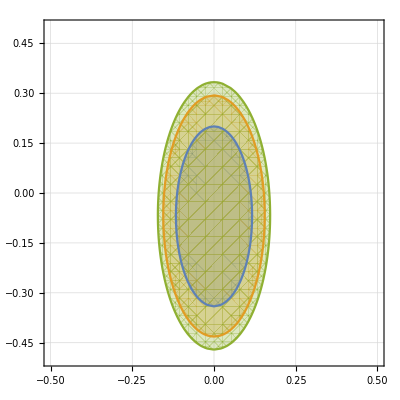

```mathematica
With[{x=params[[1]],y=params[[2]]},
	RegionPlot[
		{
			{x,y}∈reg68,
			{x,y}∈reg90,
			{x,y}∈reg95
		}
		,
		{x,-0.5,0.5},{y,-0.5,0.5}
		,
		Background->White,
		GridLines->Automatic
	]
]
```

#### correct

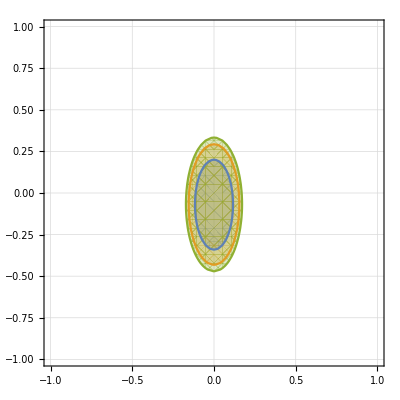

#### previous

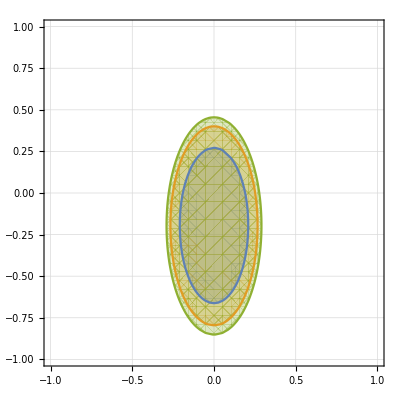

## PlotConfidenceRegion

```mathematica
?PlotConfidenceRegion
```

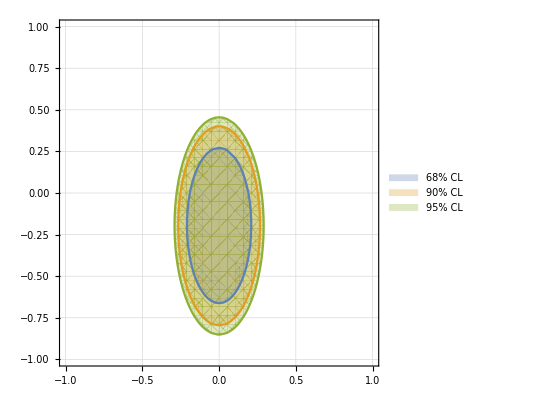

```mathematica
PlotConfidenceRegion[
	{reg68,reg90,reg95},
	{-1,+1},{-1,+1}
	,
	(* Options *)
	PlotLegends->{"68% CL","90% CL", "95% CL"},
	GridLines->Automatic
]
```

## PlotConfidenceIntervals

```mathematica
params1={
	WC["lq1",{3,3,3,3}],
	WC["lequ3",{3,3,2,2}],
	WC["lq1",{3,3,2,3}],
	WC["ed",{3,3,2,3}],
	WC["ledq",{3,3,2,3}]
};
regs=ConfidenceRegion[χττSMEFT,{#},{},0.90]&/@params1;
```

```mathematica
?PlotConfidenceIntervals
```

𝒞_lq_3333^(1) : {{-1.38601,0.602023}}

𝒞_lequ_3322^(3) : {{-0.219906,0.219906}}

𝒞_lq_3323^(1) : {{-0.425511,0.425511}}

𝒞_ed_3323 : {{-0.425511,0.425511}}

𝒞_ledq_3323 : {{-0.471431,0.471431}}

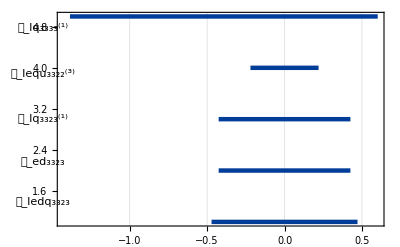

```mathematica
PlotConfidenceIntervals[regs]
```

## Export χ^2 using WCxf

To be added later.

## CLs method

Do we really want to do this?

## Options and auxiliary functions

## Basic expressions

### Particles

#### Fermions

```mathematica
?e
```

```mathematica
?ν
```

```mathematica
?u
```

```mathematica
?d
```

#### Gauge bosons

```mathematica
?Photon
```

```mathematica
?ZBoson
```

```mathematica
?WBoson
```

### Wilson coefficients

```mathematica
?WC
```

#### Printing

```mathematica
WC["ledq",{3,3,2,2}]
%//TraditionalForm
```

WC[ledq,{3,3,2,2}]

𝒞_ledq_3322

### Form factors

```mathematica
?FF
```

#### Printing

```mathematica
FF[Vector,{"regular",{0,0}},{Left,Right},{e[3],e[3],u[2],u[2]}]
%//TraditionalForm
```

FF[Vector,{regular,{0,0}},{Left,Right},{e[3],e[3],u[2],u[2]}]

[F_(V{reg,{0,0}})^LR]_(u[2]u[2])^(e[3]e[3])

#### Lorentz structures

```mathematica
?Scalar
```

```mathematica
?Vector
```

```mathematica
?Tensor
```

```mathematica
?DipoleL
```

```mathematica
?DipoleQ
```

### Parameters

This whole section needs some modifications probably!

```mathematica
?Mass
```

```mathematica
?Width
```

```mathematica
?DefineParameters
```

```mathematica
?GetParameters
```

```mathematica
GetParameters[]
```

<|αEM→0.00781861,VEV→246.221,sW→0.483424,cW→0.875386,Mass[ZBoson]→91.1876,Width[ZBoson]→2.4952,Mass[WBoson]→79.8244,Width[WBoson]→2.085,Mass[Photon]→0,Width[Photon]→0,V[ud]→0.974349,V[us]→0.2265,V[ub]→0.00132842-0.00336345 ⅈ,V[cd]→-0.2265,V[cs]→0.974349,V[cb]→0.0405288,V[td]→0.00785135-0.00336345 ⅈ,V[ts]→-0.0405288,V[tb]→1,HighPTio`Parameters`PackagePrivate`GeV2toPB→3.89379×10^8|>

## NP models

To be added later...

## Form factor matching to the SMEFT

### Function to match the form factors to the SMEFT

```mathematica
?MatchToSMEFT
```

### Defining the global settings for the EFT power counting

#### EFT series truncation

```mathematica
?SetEFTorder
```

```mathematica
?GetEFTorder
```

#### EFT operator mass dimension

```mathematica
?SetOperatorDimension
```

```mathematica
?GetOperatorDimension
```

## Options

### PTcuts

```mathematica
?PTcuts
```

### MLLcuts

```mathematica
?MLLcuts
```

### EFTorder

```mathematica
?EFTorder
```

### OperatorDimension

```mathematica
?OperatorDimension
```

### OutputFormat

```mathematica
?OutputFormat
```

### Coefficients

```mathematica
?Coefficients
```

### Luminosity

```mathematica
?Luminosity
```

## WCxf

```mathematica
wc=WC["lq1",{3,2,1,1}];
wc//TraditionalForm
```

Conjugate[𝒞_lq_2311^(1)]

```mathematica
wc/.MapToWCxf
```

Conjugate[WCxf[lq1_2311]]

```mathematica
wc1=WC["eq",{3,2,1,1}];
wc1//TraditionalForm
wc1/.MapToWCxf
```

Conjugate[𝒞_eq_2311]

Conjugate[WCxf[qe_1123]]